```mathematica
tmin[m12_,m22_,m32_,m42_,s_]:=
Module[{e1cm,p1cm,e2cm,p2cm,e3cm,p3cm,e4cm,p4cm},
    e1cm=(s+m12-m22)/(2*Sqrt[s]); 
    p1cm=Sqrt[e1cm^2-m12];
     e2cm=(s+m22-m12)/(2*Sqrt[s]);
     p2cm=Sqrt[e2cm^2-m22];
     e3cm=(s+m32-m42)/(2*Sqrt[s]);
     p3cm=Sqrt[e3cm^2-m32];
     e4cm=(s+m42-m32)/(2*Sqrt[s]);
      p4cm=Sqrt[e4cm^2-m42];  
(m12-m32-m22+m42)^2/4/s-(p2cm-p4cm)^2];
tminq[q2_,xB_,mmeson_,mtarget_]:=
tmin[-q2,mtarget^2,mmeson^2,mtarget^2,-q2+q2/xB+mtarget^2];
w2[q2_,xb_]:=(1/xb-1)*q2+mp^2;
e2cm[q2_,xb_]:= (w2[q2,xb]+mp^2+q2)/2/Sqrt[w2[q2,xb]];
```

```mathematica
q2=3.77; xb=0.513; 
tminq[q2,xb,meta,mp]
```

-0.523257

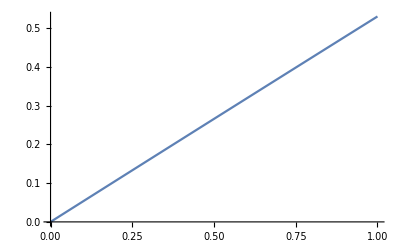

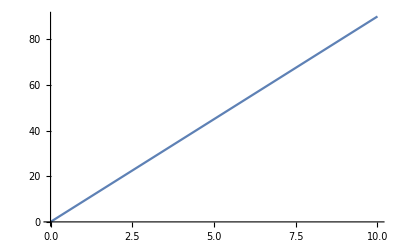

-Graphics3D-

-Graphics3D-

```mathematica
Plot[e2cm[q2,0.99]-mp,{q2,0,1},ImageSize->Full] 

Plot[w2[q2,0.1]-mp^2,{q2,0,10},ImageSize->Full]


Plot3D[e2cm[q2,xb]-mp,{q2,0.,5.},{xb,0.,1.0},ColorFunction->"SunsetColors",PlotLegends->Automatic]
Plot3D[w2[q2,xb]-mp,{q2,0.,5.},{xb,0.,1.0},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```